# Neural Logic

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]]]
```

```mathematica
?neurallogic`*
```

```mathematica
DifferentiableHardIfThenElse[w,b1,b2]
```

1-Max[1-Max[b1,1-w],1-Max[b2,w]]

```mathematica
Manipulate[Plot[DifferentiableHardIfThenElse[w,b1,b2],{w,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],{b1,0,1},{b2,0,1}]
```

```mathematica
Manipulate[Plot[DifferentiableHardIfThenElse[w,b1,b2],{b1,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],{w,0,1},{b2,0,1}]
```

```mathematica
Manipulate[Plot[DifferentiableHardIfThenElse[w,b1,b2],{b2,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],{w,0,1},{b1,0,1}]
```

```mathematica
PiecewiseExpand[DifferentiableHardIfThenElse[w,b1,b2]]
```

Piecewise[{{b1, (b2-w≥0&&b1+w≥1&&b1-b2≤0)||(b2-w<0&&b1+w≥1&&b1-w≤0)}, {b2, (b2-w≥0&&b1+w≥1&&b1-b2>0)||(b2-w≥0&&b1+w<1&&b2+w<1)}, {1-w, (b2-w≥0&&b1+w<1&&b2+w≥1)||(b2-w<0&&w≥1/2&&b1+w<1)}, {w, True}}]

```mathematica
FullSimplify[PiecewiseExpand[DifferentiableHardIfThenElse[w,b1,b2](*,Assumptions->w>=0&&w<=1&&b1>=0&&b1<=1&&b2>=0&&b2<=1*)]]
```

Piecewise[{{b1, (b2≥w||b1≤w)&&(b2<w||b1≤b2)&&b1+w≥1}, {b2, b2≥w&&(b1+w≥1||b2+w<1)&&(b1+w<1||b1>b2)}, {1-w, (b2≥w||2 w≥1)&&(b2<w||b2+w≥1)&&b1+w<1}, {w, True}}]

```mathematica
ite=IfThenElseLayer[]
```

NetGraph[<>]

```mathematica
ite[{0.25,0.2,0.8}]
```

0.75

```mathematica
ite[{0.75,0.2,0.8}]
```

0.25

```mathematica
ite[{{0.25,0.25},{0.2,0.2},{0.8,0.8}}]
```

{0.75,0.75}

```mathematica
ite[{{0.25,0.75},{0.2,0.2},{0.8,0.8}}]
```

{0.75,0.25}

```mathematica
ite[{{0.25,0.75},{0.2,0.6},{0.7,0.3}}]
```

{0.7,0.6}

```mathematica
ite[{{0.25,0.75,0.001},{0.2,0.6,0.49},{0.7,0.3,0.51}}]
```

{0.7,0.6,0.51}

```mathematica
ite[{(* If *){1,1},(* IfTrue *){0.2,0.6},(* IfFalse *){0.7,0.3}}]
```

{0.2,0.6}

```mathematica
ite[{(* If *){1,0},(* IfTrue *){0.2,0.6},(* IfFalse *){0.7,0.3}}]
```

{0.2,0.3}

```mathematica
ite[{(* If *){0,0},(* IfTrue *){0.2,0.6},(* IfFalse *){0.7,0.3}}]
```

{0.7,0.3}

```mathematica
ite[{(* If *){0,1},(* IfTrue *){0.2,0.6},(* IfFalse *){0.7,0.3}}]
```

{0.7,0.6}

```mathematica
ite[{(* If *){0,1},(* IfTrue *){0.2,0.6},(* IfFalse *){0.7,0.3}}]
```

{0.7,0.6}

```mathematica
ite[<|"Condition"->{1,0},"IfTrue"->{{0.1,0.2},{0.3,0.4}},"IfFalse"->{{0.6,0.7},{0.8,0.9}}|>]
```

{{0.1,0.2},{0.8,0.9}}

```mathematica
ite[<|"Condition"->{0,1},"IfTrue"->{{0.1,0.2},{0.3,0.4}},"IfFalse"->{{0.6,0.7},{0.8,0.9}}|>]
```

{{0.6,0.7},{0.3,0.4}}

```mathematica
ite[<|"Condition"->{0,0},"IfTrue"->{{0.1,0.2},{0.3,0.4}},"IfFalse"->{{0.6,0.7},{0.8,0.9}}|>]
```

{{0.6,0.7},{0.8,0.9}}

```mathematica
ite[<|"Condition"->{1,1},"IfTrue"->{{0.1,0.2},{0.3,0.4}},"IfFalse"->{{0.6,0.7},{0.8,0.9}}|>]
```

{{0.1,0.2},{0.3,0.4}}

```mathematica
Manipulate[Plot[DifferentiableHardIfThenElse[w1,b1,DifferentiableHardIfThenElse[w2,b2,b3]],{w1,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2,1},{1/2,1}},AxesLabel->Automatic],{w2,0,1},{b1,0,1},{b2,0,1},{b3,0,1}]
```

```mathematica
ft=FirstTrue[]
```

NetFoldOperator[<>]

```mathematica
ft[{0.1,0.2,0.8,0.8,0.6,0.1}]
```

<|SoftBits→{0.,0.,0.8,0.,0.,0.},Output→{0.,0.,1.,1.,1.,1.}|>

```mathematica
ft[{0.1,0.51,0.3,0.2,0.9,0.9}]
```

<|SoftBits→{0.,0.51,0.,0.,0.,0.},Output→{0.,1.,1.,1.,1.,1.}|>

```mathematica
ft[{0.1,0.51,0.63,0.72,0.9,0.9}]
```

<|SoftBits→{0.,0.51,0.,0.,0.,0.},Output→{0.,1.,1.,1.,1.,1.}|>

```mathematica
ft[{0.9,0.1,0.3,0.2,0.9,0.1}]
```

<|SoftBits→{0.9,0.,0.,0.,0.,0.},Output→{1.,1.,1.,1.,1.,1.}|>

```mathematica
hndl=HardNeuralDecisionList[3,5,4][[1]]
```

NetGraph[<>]

```mathematica
hndl[{1,0,1}]
```

<|Output→{0.330995,0.336824,0.343466,0.260503},Ignore→{1.,1.,1.,1.,1.}|>

```mathematica
hndl[{0.51,0.4,0}]
```

<|Output→{0.293414,0.298581,0.304469,0.230925},Ignore→{1.,1.,1.,1.,1.}|>

```mathematica
hndl[{1,0,1}]
```

<|Output→{0.330995,0.336824,0.343466,0.260503},Ignore→{1.,1.,1.,1.,1.}|>

```mathematica
hndl[{0.1,0,0.9}]
```

<|Output→{0.295298,0.29785,0.259595,0.341853},Ignore→{0.,1.,1.,1.,1.}|>

```mathematica
hndl[{0,0,1}]
```

<|Output→{0.295298,0.29785,0.259595,0.341853},Ignore→{0.,1.,1.,1.,1.}|>

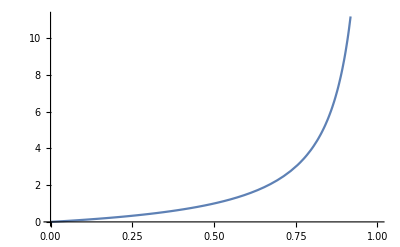

```mathematica
Plot[x/(1-x),{x,0,1}]
```